# An Introduction to Adiabatic Quantum Computing

In addition to the circuit model discussed in the textbook, adiabatic quantum computing (ACQ) shows great promise as a computing platform. ACQ does not require a description in terms of gates and circuit components, nevertheless, the circuit model and ACQ do share common features and it has been argued that the latter is a special case of the former 1

The philosophy behind ACQ is similar to that of classical simulated annealing2. Consider a complicated multivariate function f(x_1...x_n). The goal of simulated annealing is to find the point x_1^⋆... x_n^⋆ in which this function has its extremum (usually minimum) value. This is achieved by relying on statistical and thermodynamic arguments to simulate a physical system that evolves into the desired configuration.

Typically, the goal of ACQ is to find the ground state (energy eigenstate with the lowest energy) of a quantum system by simulating, on the computer, Hamiltonian evolution of the latter. Problems of this type are important in many applications. For example, finding the ground state of large molecules can require tremendous time and memory resources on standard digital computers. The latter problem has many applications, including drug design and in the understanding of protein folding to name just a few. A functional quantum computer could greatly advance our capabilities in these arenas.

The goal of ACQ is simple. Given a quantum system that is described by a Hamiltonian H, find its ground state energy eigenvalue and eigenstate.  To achieve the desired goal; one takes advantage of the quantum adiabatic theorem,  which we paraphrase (for the special case of the ground state) below

### Quantum Adiabatic Theorem

Consider a quantum system that is described by a Hamiltonian H(t) that evolves very slowly (i.e. adiabatically ) in time t.  If this system possesses a non-degenerate ground state |ψ(t_0) ⟩ at t=t_0,  then e^(i γ)|ψ(t)⟩, where |ψ(t)⟩ is an instantaneous ground eigenstate of H(t), is a solution to the Schrodinger equation. The phase e^(i γ)=⟨ψ(t)|U(t,t_0)|ψ(t_0)⟩/ |⟨ψ(t)|U(t,t_0)|ψ(t_0)⟩| and  U(t,t_0) is the time evolution operator.

From our previous discussions, we know that this theorem obviously applies to the case where H is independent of time. The question is, how slow must H(t) evolve in order for the above statement to hold? We will not address that question here, instead we will experiment with a model system in order to illustrate the point.

### The AQC Strategy

We exploit the quantum adiabatic theorem by mapping the time independent Hamiltonian H, whose ground state is sought, into a time dependent Hamiltonian H(t)
H(t)=H_0(1-t/T) + t/T  H.

Here, H_0is a Hamiltonian whose eigenstates and eigenvalues we can easily discover, and T is a parameter. At t=0 we find that H(0)=H_0  and at t =T,  H(T)=H. So according to the adiabatic theorem if we start at t=0 in the ground state of H_0 we are guaranteed, up to a phase factor, to wind up in the ground state at t=T . As the utility of the adiabatic theorem is contingent on adiabatic evolution, we take the time derivative of H(t)

d H(t)/dt = -H_0/T+ H/T

and which suggests that slow evolution implies large values for the parameter T.

### Model System

```mathematica
(* define basic 1-qubit gates *)
```

```mathematica
ClearAll["Global`*"];
σX={{0,1},{1,0}};
σZ={{1,0},{0,-1}};
σY={{0,-I},{I,0}};
unit={{1,0},{0,1}};
```

We wish to find the ground state of the following Hamiltonian

```mathematica
H1=ℏω (KroneckerProduct[σX,unit,unit]-KroneckerProduct[unit,σX,unit]+KroneckerProduct[unit,unit,σX]);
Hint=ℏΩ (KroneckerProduct[σX,σX,unit]+ KroneckerProduct[σX,unit,σX]+  KroneckerProduct[unit,σX,σX]);
```

```mathematica
H=H1+Hint;
MatrixForm[H]
```

(0 | ℏω | -ℏω | ℏΩ | ℏω | ℏΩ | ℏΩ | 0
ℏω | 0 | ℏΩ | -ℏω | ℏΩ | ℏω | 0 | ℏΩ
-ℏω | ℏΩ | 0 | ℏω | ℏΩ | 0 | ℏω | ℏΩ
ℏΩ | -ℏω | ℏω | 0 | 0 | ℏΩ | ℏΩ | ℏω
ℏω | ℏΩ | ℏΩ | 0 | 0 | ℏω | -ℏω | ℏΩ
ℏΩ | ℏω | 0 | ℏΩ | ℏω | 0 | ℏΩ | -ℏω
ℏΩ | 0 | ℏω | ℏΩ | -ℏω | ℏΩ | 0 | ℏω
0 | ℏΩ | ℏΩ | ℏω | ℏΩ | -ℏω | ℏω | 0)

We find the ground state of this Hamiltonian by introducing Hamiltonian H_0


whose eigenstates are easy to calculate. For example in this case, the eigenstates of H_0 are simply the 3-qubit computational basis vectors (|0 ⟩)_3, (|1 ⟩)_3 ,... |7⟩_3. The ground state of  H_0 is |7⟩_3 with eigenvalue -3ℏω.

```mathematica
H0=ℏω (KroneckerProduct[σZ,unit,unit]+KroneckerProduct[unit,σZ,unit]+KroneckerProduct[unit,unit,σZ]);
MatrixForm[H0]
```

(3 ℏω | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏω | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ℏω | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ℏω | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏω | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ℏω | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ℏω | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 ℏω)

```mathematica
(* now we construct the adiabatic hamiltonian *)
Had[t_,T_]=(1-t/T)H0+ t/T H ;
% // MatrixForm
```

(3 (1-t/T) ℏω | (t ℏω)/T | -(t ℏω)/T | (t ℏΩ)/T | (t ℏω)/T | (t ℏΩ)/T | (t ℏΩ)/T | 0
(t ℏω)/T | (1-t/T) ℏω | (t ℏΩ)/T | -(t ℏω)/T | (t ℏΩ)/T | (t ℏω)/T | 0 | (t ℏΩ)/T
-(t ℏω)/T | (t ℏΩ)/T | (1-t/T) ℏω | (t ℏω)/T | (t ℏΩ)/T | 0 | (t ℏω)/T | (t ℏΩ)/T
(t ℏΩ)/T | -(t ℏω)/T | (t ℏω)/T | -(1-t/T) ℏω | 0 | (t ℏΩ)/T | (t ℏΩ)/T | (t ℏω)/T
(t ℏω)/T | (t ℏΩ)/T | (t ℏΩ)/T | 0 | (1-t/T) ℏω | (t ℏω)/T | -(t ℏω)/T | (t ℏΩ)/T
(t ℏΩ)/T | (t ℏω)/T | 0 | (t ℏΩ)/T | (t ℏω)/T | -(1-t/T) ℏω | (t ℏΩ)/T | -(t ℏω)/T
(t ℏΩ)/T | 0 | (t ℏω)/T | (t ℏΩ)/T | -(t ℏω)/T | (t ℏΩ)/T | -(1-t/T) ℏω | (t ℏω)/T
0 | (t ℏΩ)/T | (t ℏΩ)/T | (t ℏω)/T | (t ℏΩ)/T | -(t ℏω)/T | (t ℏω)/T | -3 (1-t/T) ℏω)

### Exact Diagonalization

Before we embark on an adiabatic journey with this Hamiltonian, let’s find, using standard methods, the instantaneous eigenvalues of H(t) for all values of t. This includes the sought for eigenvalue H(T) . Because we are working with a 3-qubit system, standard matrix diagonalization is computationally straightforward. However this become computationally intractable for Hamiltonians in a  large Hilbert space (e.g. for a 100 qubits). As we illustrate below, quantum adiabatic evolution offers an alternative path toward this goal.

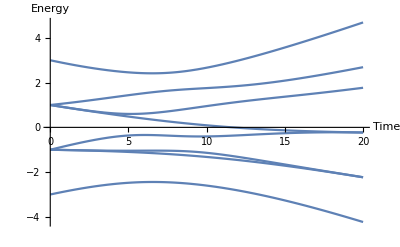

```mathematica
(* We set the parameters ℏω, ℏΩ to some arbitrary values, and take the value for T=20 *)
ℏω=1.0;ℏΩ=1.23;
Tend=20.0;
Plot[Sort[Eigenvalues[Had[t,Tend]]],{t,0,Tend},PlotRange->All,AxesLabel->{Time,Energy}]
```

The above graph is a plot of all eigenvalues, shown on the vertical axis, of H(t) for all values of 0 < t < T on the horizontal axis.
The bottom-most curve represent the ground state energy as a function of t.

### Quantum Adiabatic Evolution

We now employ quantum adiabatic evolution to estimate the ground state wavefunction and energy eigenvalue at t=T. First, we express the system wavefunction as an expansion over the computational basis of the 3-qubit Hilbert space, i.e.


or, as a matrix representation

```mathematica
psi[t_]={c0[t],c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t]};
```

Inserting this expression into the Schrodinger equation, we obtain a set of coupled equations for the coefficients c_i(t).

```mathematica
equations=Had[t,T].psi[t]-I  psi'[t];
```

```mathematica
set[T_]=Table[equations[[i]]==0,{i,1,8}]
```

{3. (1-t/T) c0[t]+(1. t c1[t])/T-(1. t c2[t])/T+(1.23 t c3[t])/T+(1. t c4[t])/T+(1.23 t c5[t])/T+(1.23 t c6[t])/T-ⅈ c0'[t]==0,(1. t c0[t])/T+1. (1-t/T) c1[t]+(1.23 t c2[t])/T-(1. t c3[t])/T+(1.23 t c4[t])/T+(1. t c5[t])/T+(1.23 t c7[t])/T-ⅈ c1'[t]==0,-(1. t c0[t])/T+(1.23 t c1[t])/T+1. (1-t/T) c2[t]+(1. t c3[t])/T+(1.23 t c4[t])/T+(1. t c6[t])/T+(1.23 t c7[t])/T-ⅈ c2'[t]==0,(1.23 t c0[t])/T-(1. t c1[t])/T+(1. t c2[t])/T-1. (1-t/T) c3[t]+(1.23 t c5[t])/T+(1.23 t c6[t])/T+(1. t c7[t])/T-ⅈ c3'[t]==0,(1. t c0[t])/T+(1.23 t c1[t])/T+(1.23 t c2[t])/T+1. (1-t/T) c4[t]+(1. t c5[t])/T-(1. t c6[t])/T+(1.23 t c7[t])/T-ⅈ c4'[t]==0,(1.23 t c0[t])/T+(1. t c1[t])/T+(1.23 t c3[t])/T+(1. t c4[t])/T-1. (1-t/T) c5[t]+(1.23 t c6[t])/T-(1. t c7[t])/T-ⅈ c5'[t]==0,(1.23 t c0[t])/T+(1. t c2[t])/T+(1.23 t c3[t])/T-(1. t c4[t])/T+(1.23 t c5[t])/T-1. (1-t/T) c6[t]+(1. t c7[t])/T-ⅈ c6'[t]==0,(1.23 t c1[t])/T+(1.23 t c2[t])/T+(1. t c3[t])/T+(1.23 t c4[t])/T-(1. t c5[t])/T+(1. t c6[t])/T-3. (1-t/T) c7[t]-ⅈ c7'[t]==0}

These coupled first order equations are now solved, starting from the initial ground state at t=0, for the ground state amplitude at
t=T. Since at t=0, the ground state amplitude is the basis ket  (|7⟩)_3 or |111⟩,

```mathematica
groundinitial={0,0,0,0,0,0,0,1};
H0.groundinitial==-3 groundinitial
```

True

```mathematica
total=Flatten[Append[set[Tend],{c0[0]==0,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==1}]];
```

which we now solve using the NDSOLVE command.

```mathematica
sols=Flatten[NDSolve[total,{c0,c1,c2,c3,c4,c5,c6,c7},{t,0,Tend}]];
```

```mathematica
wave[t_]=psi[t] /. sols;
```

### Solution to Adiabatic Evolution.

The adiabatic wavefunction |ψ(t)⟩ is contained in the wavefunction wave[t]

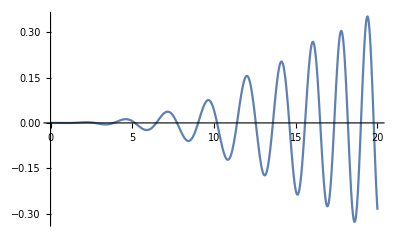
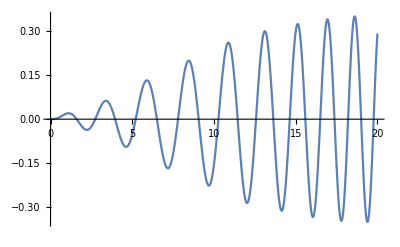
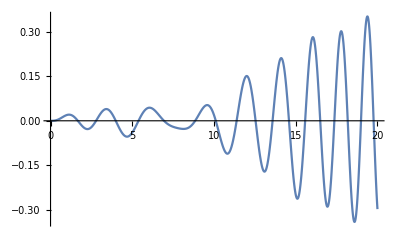
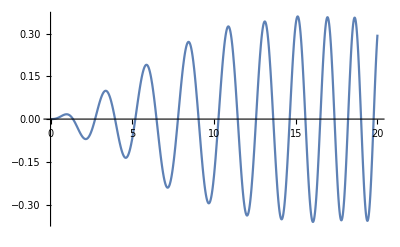
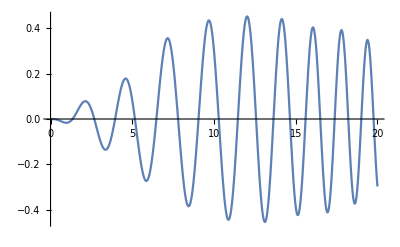
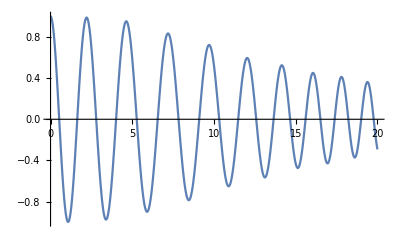
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[Re[wave[t][[i]]],{t,0,Tend}],{i,1,8}]
```

This diagram plots the real part of the amplitude, as a function of time, for each basis component of the amplitude. Note that at t=0 all amplitudes,
save for the graph with i=7 which corresponds to the initial ground state wavefunction, vanishes. At   t=T  all components are occupied. 
We can estimate the energy eigenvalue of the ground state by evaluating

E_ground ≈⟨ψ(T)| H | ψ(T)⟩

```mathematica
Conjugate[wave[Tend]].H.wave[Tend]
```

-4.22956+8.32667×10^-17 ⅈ

Let’s compare this estimate with the exact result, using Mathematica’s Eigenvalues routine

```mathematica
?Eigenvalues
Eigenvalues[H]
```

RowBox[{"Eigenvalues", "[", StyleBox["m", "TI"], "]"}] gives a list of the eigenvalues of the square matrix StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] gives the generalized eigenvalues of StyleBox["m", "TI"] with respect to StyleBox["a", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] eigenvalues of StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] generalized eigenvalues.

{4.69,-4.23,2.69,-2.23,-2.23,1.77,-0.23,-0.23}

Notice that the lowest (i.e. ground state), exact eigenvalue has the value E = - 4.23, within 0.005 the value obtained using adiabatic evolution.

### Quantum Supremacy

In the 3-qubit example given above, we demonstrated how quantum adiabatic evolution can be used to estimate the ground energy eigenvalue. 
In order to arrive at our estimate we needed to solve the time dependent Schrodinger equation for the system. This is not very efficient, indeed imagine solving a set of (2^100) coupled equations in a 100 qubit system. So what advantages are conferred by quantum adiabatic evolution? If we simulate the latter with a classical computer, as done here, there are no advantages. But for a real quantum system containing, let’s say a 100 qubits, all we need to do is encode the Hamiltonian H, load the initial ground state |ψ(0)⟩ and simply allow the system to evolve according to Postulate V discussed in the text. In this way, the quantum computer effectively, and with a modest 100 qubit overhead, targets the solution that we harvest by interrogating the qubits at t=T.

1	"Adiabatic Quantum Computation is equivalent to Standard Quantum Computation", D. Aharonov et. al, arXiv:quant-ph/0405098

2	https:/en.wikipedia.org/wiki/Simulated_annealing